```mathematica
Remove["Global`*"]
```

# Optical transfer-matrix method

## Calculates reflectance, transmittance and absorptance for a thin-film stack

## Generalized TMM

```mathematica
TMM[stack_,λ_,θi_,pol_]:=
Module[{ns,ds,θs,δs,r,rs,t,ts,Mn,M,rstack,tstack,R,T},
{ns,ds}=Transpose[stack];
θs=FoldList[ArcSin[#2Sin[#1]]&,θi,#[[1]]/#[[2]]&/@Partition[ns,2,1]];
δs=(2π ns ds Cos[θs])/λ;
r=Which[StringMatchQ[pol,"s"],(#1[[1]] Cos[#2[[1]]]-#1[[2]] Cos[#2[[2]]])/(#1[[1]] Cos[#2[[1]]]+#1[[2]] Cos[#2[[2]]])&,StringMatchQ[pol,"p"],(#1[[2]] Cos[#2[[1]]]-#1[[1]] Cos[#2[[2]]])/(#1[[2]] Cos[#2[[1]]]+#1[[1]] Cos[#2[[2]]])&];
rs=MapThread[r,{Partition[ns,2,1],Partition[θs,2,1]}];
t=Which[StringMatchQ[pol,"s"],(2#1[[1]]Cos[#2[[1]]])/(#1[[1]]Cos[#2[[1]]]+#1[[2]]Cos[#2[[2]]])&,StringMatchQ[pol,"p"],(2#1[[1]]Cos[#2[[1]]])/(#1[[2]]Cos[#2[[1]]]+#1[[1]]Cos[#2[[2]]])&];
ts=MapThread[t,{Partition[ns,2,1],Partition[θs,2,1]}];
Mn=MapThread[({{Exp[-ⅈ #1], #2Exp[ⅈ#1]}, {#2Exp[-ⅈ#1], Exp[ⅈ#1]}})1/#3&,{Rest[Most[δs]],Most[rs],Most[ts]}];
M=Fold[Dot,IdentityMatrix[2],Mn].(({{1, Last[rs]}, {Last[rs], 1}})1/Last[ts]);
rstack=M[[2,1]]/M[[1,1]];
tstack=1/M[[1,1]];
R=Abs[rstack]^2;
T=Which[StringMatchQ[pol,"s"],Abs[tstack]^2 Re[Last[ns]Cos[Last[θs]]]/Re[First[ns]Cos[First[θs]]],StringMatchQ[pol,"p"],Abs[tstack]^2 Re[Last[ns]Cos[Conjugate[Last[θs]]]]/Re[First[ns]Cos[Conjugate[First[θs]]]]];
{R,T,1-R-T}
]
```

## Three-layer TMM

```mathematica
layer3[stack_,λ_,θ_,pol_]:=
Module[{ns,ds,θs,δs,r,rs,t,ts,rstack,tstack,R,T},
{ns,ds}=Transpose[stack];
θs=FoldList[ArcSin[#2Sin[#1]]&,θ,#[[1]]/#[[2]]&/@Partition[ns,2,1]];
δs=(2π ns ds Cos[θs])/λ;
r=Which[StringMatchQ[pol,"s"],(#1[[1]] Cos[#2[[1]]]-#1[[2]] Cos[#2[[2]]])/(#1[[1]] Cos[#2[[1]]]+#1[[2]] Cos[#2[[2]]])&,StringMatchQ[pol,"p"],(#1[[2]] Cos[#2[[1]]]-#1[[1]] Cos[#2[[2]]])/(#1[[2]] Cos[#2[[1]]]+#1[[1]] Cos[#2[[2]]])&];
rs=MapThread[r,{Partition[ns,2,1],Partition[θs,2,1]}];
t=Which[StringMatchQ[pol,"s"],(2#1[[1]]Cos[#2[[1]]])/(#1[[1]]Cos[#2[[1]]]+#1[[2]]Cos[#2[[2]]])&,StringMatchQ[pol,"p"],(2#1[[1]]Cos[#2[[1]]])/(#1[[2]]Cos[#2[[1]]]+#1[[1]]Cos[#2[[2]]])&];
ts=MapThread[t,{Partition[ns,2,1],Partition[θs,2,1]}];
rstack=(rs[[1]]+ⅇ^(2 ⅈ δs[[2]]) rs[[2]])/(1+ⅇ^(2 ⅈ δs[[2]]) rs[[1]] rs[[2]]);
tstack=(ⅇ^(ⅈ δs[[2]]) ts[[1]] ts[[2]])/(1+ⅇ^(2 ⅈ δs[[2]]) rs[[1]] rs[[2]]);
R=Abs[rstack]^2;
T=Which[StringMatchQ[pol,"s"],Abs[tstack]^2 Re[Last[ns]Cos[Last[θs]]]/Re[First[ns]Cos[First[θs]]],StringMatchQ[pol,"p"],Abs[tstack]^2 Re[Last[ns]Cos[Conjugate[Last[θs]]]]/Re[First[ns]Cos[Conjugate[First[θs]]]]];
{R,T,1-R-T}
]
```

## Four-layer TMM

```mathematica
layer4[stack_,λ_,θ_,pol_]:=
Module[{ns,ds,θs,δs,r,rs,t,ts,rstack,tstack,R,T},
{ns,ds}=Transpose[stack];
θs=FoldList[ArcSin[#2Sin[#1]]&,θ,#[[1]]/#[[2]]&/@Partition[ns,2,1]];
δs=(2π ns ds Cos[θs])/λ;
r=Which[StringMatchQ[pol,"s"],(#1[[1]] Cos[#2[[1]]]-#1[[2]] Cos[#2[[2]]])/(#1[[1]] Cos[#2[[1]]]+#1[[2]] Cos[#2[[2]]])&,StringMatchQ[pol,"p"],(#1[[2]] Cos[#2[[1]]]-#1[[1]] Cos[#2[[2]]])/(#1[[2]] Cos[#2[[1]]]+#1[[1]] Cos[#2[[2]]])&];
rs=MapThread[r,{Partition[ns,2,1],Partition[θs,2,1]}];
t=Which[StringMatchQ[pol,"s"],(2#1[[1]]Cos[#2[[1]]])/(#1[[1]]Cos[#2[[1]]]+#1[[2]]Cos[#2[[2]]])&,StringMatchQ[pol,"p"],(2#1[[1]]Cos[#2[[1]]])/(#1[[2]]Cos[#2[[1]]]+#1[[1]]Cos[#2[[2]]])&];
ts=MapThread[t,{Partition[ns,2,1],Partition[θs,2,1]}];
rstack=(rs[[1]]+ⅇ^(2 ⅈ δs[[2]]) rs[[2]]+ⅇ^(2 ⅈ δs[[3]]) (ⅇ^(2 ⅈ δs[[2]])+rs[[1]] rs[[2]]) rs[[3]])/(1+ⅇ^(2 ⅈ δs[[2]]) rs[[1]] rs[[2]]+ⅇ^(2 ⅈ δs[[3]]) (ⅇ^(2 ⅈ δs[[2]]) rs[[1]]+rs[[2]]) rs[[3]]);
tstack=(ⅇ^(ⅈ (δs[[2]]+δs[[3]])) ts[[1]] ts[[2]] ts[[3]])/(1+ⅇ^(2 ⅈ δs[[2]]) rs[[1]] rs[[2]]+ⅇ^(2 ⅈ δs[[3]]) (ⅇ^(2 ⅈ δs[[2]]) rs[[1]]+rs[[2]]) rs[[3]]);
R=Abs[rstack]^2;
T=Which[StringMatchQ[pol,"s"],Abs[tstack]^2 Re[Last[ns]Cos[Last[θs]]]/Re[First[ns]Cos[First[θs]]],StringMatchQ[pol,"p"],Abs[tstack]^2 Re[Last[ns]Cos[Conjugate[Last[θs]]]]/Re[First[ns]Cos[Conjugate[First[θs]]]]];
{R,T,1-R-T}
]
```

## Examples

### Fabry-Perot etalon (sweep a layer thickness)

```mathematica
air={1,0};
etalon={20,d};
```

```mathematica
fpStack={air,etalon,air};
```

```mathematica
λ=500;
θ=0;
pol="s";
```

```mathematica
{Rfp,Tfp,Afp}=layer3[fpStack,λ,θ,pol];
```

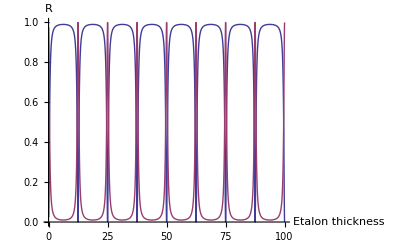

```mathematica
Plot[{Rfp,Tfp},{d,(4λ)/etalon[[1]],λ/(400etalon[[1]])},PlotRange->Full,AxesLabel->{"Etalon thickness","R"}]
```

### Surface plasmon coupling (sweep angle of incidence)

```mathematica
silicon={Sqrt[12.295],0};
dielectric={Sqrt[2.66],1.2};
gold={Sqrt[-70.72+ⅈ 7.06],0};
```

```mathematica
sppStack={silicon,dielectric,gold};
```

```mathematica
λ=1.319;
pol="p";
```

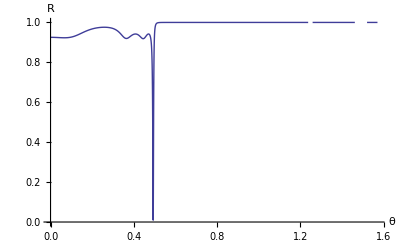

```mathematica
Plot[layer3[sppStack,λ,θ,pol][[1]],{θ,0,π/2},PlotRange->{{0,π/2},{0,1}},AxesLabel->{"θ","R"}]
```

### Lossy stack (sweep frequency and unpolarized light)

```mathematica
air={1,0};
film1={2.2,100};
film2={3.3+ⅈ 0.3,300};
```

```mathematica
lossyStack={air,film1,film2,air};
```

```mathematica
λ=10^7/k;
```

```mathematica
θ=0;
pol="s";
Rnormal=layer4[lossyStack,λ,θ,pol][[1]];
```

```mathematica
θ=π/4;
Rspol=layer4[lossyStack,λ,θ,"s"][[1]];
Rppol=layer4[lossyStack,λ,θ,"p"][[1]];
Rupol=1/2(Rspol+Rppol);
```

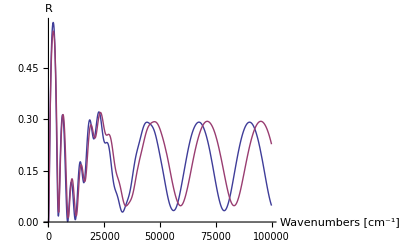

```mathematica
Plot[{Rnormal,Rupol},{k,1,100000},PlotStyle->Thick,PlotRange->Full,AxesLabel->{"Wavenumbers [cm^-1]","R"}]
```